```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];
PureIntegralsOld=ReadList[FileNameJoin[{Directory[],"files/SortetBasisFull.txt"}]];
PureIntegralsNew=PureIntegralsOld;
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
$P=2^31-1;
$P=2^31-1;
CayleyEntry[i_,j_]:=Module[{mat},
If[i==0 && j==0 ,
Return[0];
];
If[i==0 || j==0 ,
Return[1];
];

If[i==j,
mat=2msq[i]/.intMasses;
Return[mat];
];
If[i<j,
mat=((msq[i]/.intMasses)+(msq[j]/.intMasses)-Expand[(Sum[q[n],{n,i,j-1}])^2])/.mandelstamScalarProducts/.kinematics;
Return[mat];
];
If[i>j,
mat=CayleyEntry[j,i];
Return[mat];
];
]
cutCayley[mat_,l_]:=Module[{res},
res=mat;
res=Delete[res,l];
res=Transpose[Delete[Transpose[res],l]];
res
]
```

```mathematica
PureIntegralsOld[[190]]
```

ep^4 hxb[1,1,1,1,0,0,1,1,0,0,0,0,0]

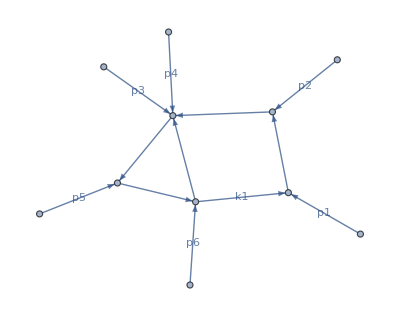

```mathematica
plotDiagram[hxb[1,1,1,1,0,0,1,1,0,0,0,0,0]]
```

# Assemble basis

```mathematica
SelectInts={7,9,75,115,131,132,133}

PureIntegralsNew=PureIntegralsOld;

PureIntegralsNew[[133]]=ep^3(mt2-s45) (s123-s56)*hxb[1,0,0,1,0,1,1,1,0,0,0,0,0](-1+2 ep)

SubPureInts=PureIntegralsNew[[SelectInts]](*/.Gram5Repl*);
Newsqrts=(Cases[SubPureInts,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
Oldsqrts=(Cases[PureIntegralsOld(*/.Gram5Repl*),root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
sqrtSetNew=Join[Oldsqrts,Newsqrts]//DeleteDuplicates;
Export[FileNameJoin[{Directory[],"files/Roots.txt"}],sqrtSetNew];
Export[FileNameJoin[{NotebookDirectory[],"TrianglePureInts.txt"}],SubPureInts];
```

{7,9,75,115,131,132,133}

ep^3 (-1+2 ep) (mt2-s45) (s123-s56) hxb[1,0,0,1,0,1,1,1,0,0,0,0,0]

{-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2}

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56),(mt2 s12-mt2 s123+s123 s345-s12 s45)^2}

# Export New Basis

```mathematica
StillNonPureInts=DeleteElements[PureIntegralsOld[[170;;]],PureIntegralsOld[[SelectIntsNotPure]]];
NewPureInts=PureIntegralsNew[[SelectIntsNotPure]];
NewBasis=Join[PureIntegralsNew[[;;169]],NewPureInts,StillNonPureInts]//EchoFunction[Length];
NewBasis=NewBasis/.Gram5Repl;
Newsqrts=(Cases[NewBasis,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
Export[FileNameJoin[{Directory[],"files/Roots.txt"}],Newsqrts];

Export[FileNameJoin[{Directory[],"files/LinearBasis-202.txt"}],NewBasis];
```

241

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56),(mt2 s12-mt2 s123+s123 s345-s12 s45)^2}

```mathematica
{152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,172,174,176,177,178,179,180,181,182,183,184,186,187,189,190,191,192,193,194,196,198,203,205,206,207,210,212,213,214,215}//Length
```

49

```mathematica
SelectInts//Length
```

134

```mathematica
SymmetricDifference[SelectInts2,SelectInts]
```

{171,175}

```mathematica
{2,3,4,7,8,9,10,11,12,14,15,16,17,18,19,20,21,22,23,24,28,32,34,35,36,37,38,39,40,41,42,43,44,45,46,47,75,76,77,78,79,80,81,82,83,84,85,86,87,88,91,92,94,95,96,97,98,103,104,105,107,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,179,180,186,187,170,174,171,175,172,176,189,190,191,192,193,194,196,203,205,206,207,177,178,181,182,183,184,198,210,212,213,214,215}//Length
```

139

```mathematica
SelectIntsNotPure//Length
```

33

```mathematica
169+33
```

202

```mathematica
PureIntegralsOld[[133]]//Factor
```

2 ep^3 (-1+2 ep) (mt2-s45) hxb[1,0,0,1,0,1,1,1,0,0,0,0,0]

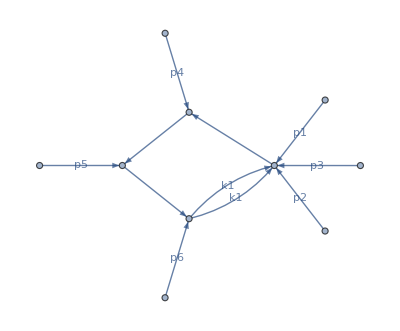

```mathematica
plotDiagram[hxb[1,0,0,1,0,1,1,1,0,0,0,0,0]]
```

```mathematica
PureIntegralsOld[[218]]
PureIntegralsOld[[219]]
PureIntegralsOld[[220]]
PureIntegralsOld[[221]]
```

ep^4 hxb[1,1,1,1,1,-1,1,1,0,0,0,0,0]

ep^4 hxb[1,1,1,1,1,0,1,1,-1,0,0,0,0]

ep^4 hxb[1,1,1,1,1,0,1,1,0,-1,0,0,0]

ep^4 hxb[1,1,1,1,1,0,1,1,0,0,0,0,0]

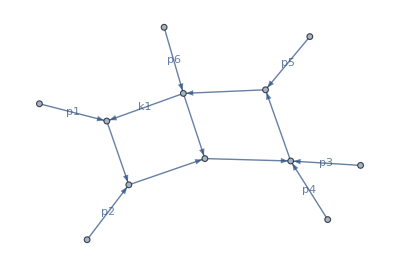

```mathematica
plotDiagram[hxb[1,1,1,1,1,0,1,1,0,-1,0,0,0]]
```